## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 3

### Reproduce frequency drift feature

#### The radius of the electron beam is given by the classical velocity, where we take the velocity to be 0.3c

```mathematica
r =(Rs+ 0.3 c tE)/Rs;
```

#### The frequency of the emitted radiation as a function of radius is (in MHz)

```mathematica
fE = 8980 √ne/10^6;
```

#### In the last problem, we found the number density as

```mathematica
ne = α/r^2+β/r^4+γ/r^6/.{α-> 3.3 10^5,β-> 4.1 10^6,γ-> 8 10^7};
```

#### The time the signal arrives at earth is given by

```mathematica
t ==  tE + (RE -Rs r)/c;
```

```mathematica
tE = Part[Solve[t ==  tE + (RE -Rs r)/c ,tE],1,1,2]
```

-1.42857 ((1. RE)/c-Rs/c-t)

```mathematica
Plot[tE/.c->1/.RE-> 1/. Rs-> 1,t]
```

System`ProtoPlotDump`iPlot[Plot,System`ProtoPlotDump`obj$11304,tE/.c→1/.RE→1/.Rs→1,t]

```mathematica
fE
```

(449 √((80000000 Rs^6)/(Rs-0.428571 c ((1. RE)/c-Rs/c-t))^6+(4.1×10^6 Rs^4)/(Rs-0.428571 c ((1. RE)/c-Rs/c-t))^4+(330000. Rs^2)/(Rs-0.428571 c ((1. RE)/c-Rs/c-t))^2))/50000

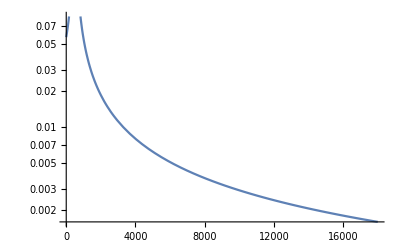

```mathematica
p0 =LogPlot[{fE /. {c-> 3 10^10,RE ->  1.5 10^13,Rs-> 6.96 10^10},f/.fv},{t,0,5 3600}]
```

```mathematica
{fE /. {c-> 3 10^8,RE ->  1.5 10^11},f/.fv}
```

ReplaceAll::reps: {fv} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{(449 √((80000000 Rs^6)/((Rs-1.28571×10^8 (500.-Rs/300000000-t))^6)+(4.1×10^6 Rs^4)/((Rs-1.28571×10^8 (500.-Rs/300000000-t))^4)+(330000. Rs^2)/((Rs-1.28571×10^8 (500.-Rs/300000000-t))^2)))/50000,f/.fv}

### Reproduce type-III radio burst dynamic spectrum

#### The time-evolution of the peak frequency of type-III radio bursts follows the empirical power law

```mathematica
f = a t^b ;
fv ={a-> 150,b-> -0.6 };
```

```mathematica
f
```

a t^b

#### The FWHM of these bursts is given by the empirical law

```mathematica
Δf = c ν;
Δfv = {c-> 0.57};
```

#### and the empirical frequency-dependent decay is

```mathematica
τD = 10^γ(10^6 ν)^-δ/. ν-> 0.02;
τDv = {γ-> 7.71,δ-> 0.95};
```

```mathematica
S=Piecewise[{{Exp[-(4 Log[2](ν - f)^2)/Δf^2] Exp[-t/τD],t >0},{0,t<0}}]
```

Piecewise[{{2^(-(4 (-a t^b+ν)^2)/(c^2 ν^2)) ⅇ^(-0.02^δ 10^(-γ+6 δ) t), t>0}, {0, True}}]

```mathematica
p1=DensityPlot[S/. fv/.Δfv /. τDv,{t,-2 3600,7 3600},{ν,0.01,10},ColorFunction->"Rainbow",PlotRange->Full,MaxRecursion->11]
```

-Graphics-

```mathematica
S/. fv/.Δfv  /. τDv
```

Piecewise[{{2^(-(12.3115 (-150/t^0.6+ν)^2)/ν^2) ⅇ^(-0.000237672 t), t>0}, {0, True}}]

```mathematica
S/. fv/.Δfv /.t-> 0
```

0

```mathematica
-1/(-10)^0.6
```

0.0776216+0.238895 ⅈ

```mathematica
Show[p0,p1]
```

-Graphics-